### Mode number to rigged configurations

```mathematica
(* Loading rigged configurations package *)
SetDirectory[NotebookDirectory[]]
<<RC.m;
(* Path ↔ Tableaux *)
ToCrystalPath[stb_]:=Block[{len=Length[stb//Flatten]},Table[{{Position[stb,k][[1,1]]}},{k,len}]];
ToTableau[path_]:=Block[{pr=path//Flatten,max},max=Max[pr];
Table[Position[pr,k]//Flatten,{k,max}]];
Quiet[Needs["Combinatorica`"]];
(* Generating rigged *)
ToRigged[SYT_,n_:5]:=rkkrec[ToCrystalPath[SYT],n];
(* generating SYT from rigged *)
ToSYT[rigged_]:=ToTableau[kkrrec[ConstantArray[{1,1},Length[rigged[[1,1]]]],rigged[[2;;3]]]];
showSYT[λT_] := Graphics[
    Table[{Text[Style[λT[[a,s]], Small, Black], 
       {s, -a}], Opacity[0.5], Lighter[Lighter[Gray]], 
      Rectangle[{s - 1/2, -a - 1/2}]}, {a, 1, Length[λT]}, 
     {s, 1, Length[λT[[a]]]}], ImageSize -> Small]; 
(* Next command includes domain of interest *)
showSYT[λT_,"DOI"]:=Graphics[
    Table[{Text[Style[λT[[a,s]], Small, Black], 
       {s, -a}], Opacity[0.5], Lighter[Lighter[Gray]], 
      Rectangle[{s - 1/2, -a - 1/2}], 
      If[MemberQ[DomainOfInterest, {a - 1, s - 1}], 
       {Gray, Rectangle[{s - 1/2, -a - 1/2}]}, 
       Nothing]}, {a, 1, Length[λT]}, 
     {s, 1, Length[λT[[a]]]}], ImageSize -> Small];
```

/home/zuxian/Documents/BAE_Project/TestFindMinimun/JuliaBifurcation

```mathematica
Cartan[a_]:=SparseArray[{Band[{1,1}]->2,Band[{2,1}]->-1,Band[{1,2}]->-1},{a,a}]
Kernel[s_]:=Array[Min[#1,#2]&,{s,s}]

(*Code taking a Young diagram and producing all admissible string length collections and the bounds on the mode numbers for these.*)
TransposeYoungD[shape_] := 
 Table[Length[Select[shape, # > i &]], {i, 0, 
   shape[[1]] - 1}](*Populating the Transpose diagram; using Volin's code*)

MAS[a_, s_, shape_] := 
 Total[shape] - Sum[shape[[b]], {b, 1, a}] - 
  Sum[TransposeYoungD[shape][[t]], {t, 1, s}] + a*s 
(*Function M_as used in article*)

AugmentedYoungD[shape_] := 
 Block[{FilledYoungD, augmented},
   augmented = 
   Prepend[shape, shape[[1]]] + 
    1(*Creating a set of right size for finding all MAS values*);
  FilledYoungD = 
   Table[MAS[i - 1, j - 1,shape], {i, 
     Length[augmented]}, {j, augmented[[i]]}];
; FilledYoungD] (*Filling the Young diagram with M_as values*)

Msetmatrix[yd_]:=Module[{Ms,Mmatrices,UpdMmatrices,M},
Ms=Delete[First/@AugmentedYoungD[yd],{{1},{-1}}];
Mmatrices=PadRight/@(Map[Replace[{x__,0..}->{x}],Table[Solve[Sum[s*M[s],{s,1,λ}]==λ,Table[M[t],{t,1,λ}],NonNegativeIntegers],{λ,Ms}]//Values ,{2}]//Tuples)(*All possible Ms sets;the index is the string length and the value is the number of strings of that length*);
Table[Module[{},UpdMmatrices=matrix ;
Append[

Prepend[UpdMmatrices,SparseArray[1->(AugmentedYoungD[yd]//First//First),Length[UpdMmatrices[[1]]]]],ConstantArray[0,Length[UpdMmatrices[[1]]]]]]

,{matrix,Mmatrices}]
]

(*AdmissibleModes[yd_] return Admissible modenumber and Msetmatrix with first and last line removed and set zero to emtyp set*)
AdmissibleModes[yd_]:=Module[{Mmatrices},
Mmatrices=Msetmatrix[yd];
Table[
Module[{Holes,M removeFirstLastZero,Holes removeFirstLastZero},

Holes=-Cartan[Length[Mmatrix]] . Mmatrix . Kernel[Length[Mmatrix[[1]]]];

Holes removeFirstLastZero=Delete[-Cartan[Length[Mmatrix]] . Mmatrix . Kernel[Length[Mmatrix[[1]]]],{{1},{-1}}];
M removeFirstLastZero=Delete[Mmatrix/.{0->{}},{{1},{-1}}];

If[AllTrue[Holes removeFirstLastZero//Flatten,GreaterEqualThan[0]],
{(Holes removeFirstLastZero+M removeFirstLastZero)/2-1/2,M removeFirstLastZero}
,Nothing]

],

{Mmatrix,Mmatrices}]//Transpose]
```

```mathematica
(*Code finding all rigged configurations for a given Young diagramme*)
ModesConfig[yd_]:=Module[{},
Modes=AdmissibleModes[yd][[1]];
Mmatrices=AdmissibleModes[yd][[2]];
Table[
Tuples[Table[Tuples[Table[Subsets[Range[-Modes[[i]][[j]][[k]],Modes[[i]][[j]][[k]]],{Mmatrices[[i]][[j]][[k]]//Total}],{k,Length[Modes[[i]][[j]]]}]],{j,Length[Modes[[i]]]}]],{i,Length[Modes]}]//Catenate]
```

```mathematica
ModestoRiggedConfig[L_,modes_]:=Module[{Mmatrix,limits,deleteFirstLastLine},
Mmatrix=PadRight[Append[Prepend[Table[Length[modes[[i,j]]],{i,Length[modes]},{j,Length[modes[[i]]]}],SparseArray[1->L,1]],{0}]];

deleteFirstLastLine[x_]:=Delete[x,{{1},{-1}}];
limits=1/2 deleteFirstLastLine[-Cartan[Length[Mmatrix]] . Mmatrix . Kernel[Length[Mmatrix[[1]]]]+Mmatrix/.{0->{}}]-1/2;

Prepend[

Append[{}]/@(Table[{Table[ConstantArray[i,Length[modes[[j,i]]]],{i,Sort[Range[Length[modes[[j]]]],Greater]}]//Catenate,Table[limits[[j,i]]+modes[[j,i,k]]+1-k,{i,Sort[Range[Length[modes[[j]]]],Greater]},{k,Length[modes[[j,i]]]}]//Catenate},{j,Length[modes]}]//Transpose)


,{ConstantArray[1,L]}]

]
```

### Functions

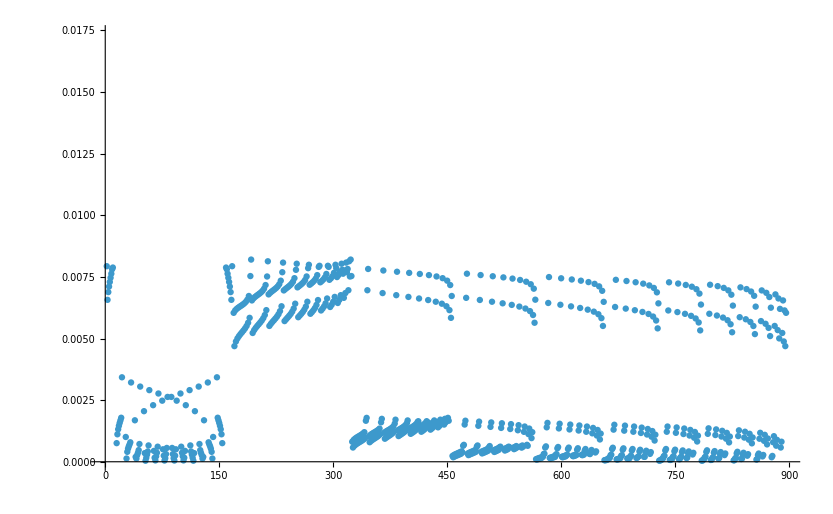

```mathematica
data1811 = Import["/home/zuxian/Documents/BAE_Project/TestFindMinimun/JuliaBifurcation/final_result/yd_13_2_1.csv"]//ToExpression;
bethe = data1811[[1]];
string = data1811[[2]];
Table[RegionHausdorffDistance[RegionUnion @@ (Point /@ Flatten[ReIm@bethe[[k]], 1]),RegionUnion @@ (Point /@ Flatten[ReIm@string[[k]], 1])],{k,Length[bethe]}]//ListPlot
```

```mathematica
loaddata[yd_, rigg_] := Module[
  {filename},
  
  filename = "/home/zuxian/Documents/BAE_Project/TestFindMinimun/JuliaBifurcation/final_result/" <> ToString[yd] <> ".csv";
  
  importdata = Round[Import[filename] // ToExpression, 10^-5] // N;
  
  lazyroots = importdata[[rigg]][[2]][[1]];
  stringroots = importdata[[rigg]][[3]];
]

HausdorffDistanceBetweenRootsM[syt_, rigg_] := Module[
  { },
  
loaddata[syt,rigg];

 hausdorffList = MapThread[
  RegionHausdorffDistance[
    Point[ReIm[#1]],
    Point[ReIm[#2]]
  ] &,
  {lazyroots, stringroots}
]
]

HausdorffDistanceBetweenRoots[yd_, rigg_] := Module[
  { },
  
loaddata[yd,rigg];

  RegionHausdorffDistance[
    RegionUnion @@ (Point /@ Flatten[ReIm@lazyroots, 1]),
    RegionUnion @@ (Point /@ Flatten[ReIm@stringroots, 1])
  ]
]

HausdorffDistanceTable[yd_] := Module[
  { points1, points2},
  
loaddata[yd,1];
  
  Table[

    lazyroots = importdata[[rigg]][[2]][[1]];
    stringroots = importdata[[rigg]][[3]];
    points1 = Point /@ Flatten[ReIm /@ lazyroots, 1];
    points2 = Point /@ Flatten[ReIm /@ stringroots, 1];
    {rigg, RegionHausdorffDistance[
       RegionUnion @@ points1,
       RegionUnion @@ points2]},
    {rigg, 1, Length[importdata]}
  ]
]

PlotHausdorffDistanceWithMean[syt_] := Module[
  {data, mean, xMin, xMax},
  data = HausdorffDistanceTable[syt];
  mean = Mean[data[[All, 2]]];
  {xMin, xMax} = MinMax[data[[All, 1]]];
  ListPlot[
    data,
    Joined -> False,
    AxesLabel -> {"Index", "Hausdorff Distance"},
    Epilog -> {
      {Red, Dashed, 
       Line[{{xMin, mean}, {xMax, mean}}]}
    }
  ]
]

RiggConfiguration[yd_, index_] := Module[
  {L, mode, label, hausdorff, rc, syt,rigg},
  loaddata[yd, index];
  L = Total[yd];
  
  mode = Import[
    "/home/zuxian/Documents/BAE_\
Project/TestFindMinimun/JuliaBifurcation/final_result/mode_" <> 
      ToString[yd] <> ".csv"
    ] // ToExpression;

  rigg = importdata[[All,1]][[index]];
  hausdorff = HausdorffDistanceBetweenRoots[yd, index];
  rc = ModestoRiggedConfig[L, mode[[rigg]]];
  syt = ToSYT[rc];
  
  Column[{
    Row[{"Rigg: ", rigg}],
    Row[{"Hausdorff Distance: ", hausdorff}],
    Style["Rigged Configuration:", Bold],
    showRC[rc],
    Style["Standard Young Tableau:", Bold],
    showSYT[syt]
  }]
]

(*plot data*)
PlotRootsComparison[yd_, rigg_, componentIndex_] := Module[
  {filename, importdata,, lazydata, stringdata},

loaddata[yd,rigg];

  (* Select data to plot **)
  lazydata = If[componentIndex === 0, DeleteCases[lazyroots, {}], {lazyroots[[componentIndex]]}];
  stringdata = If[componentIndex === 0, DeleteCases[stringroots, {}], {stringroots[[componentIndex]]}];

  (* Plot *)
  Show[
    ComplexListPlot[
      lazydata /. x_ /; NumericQ[x] :> Callout[x, x],
      PlotRange -> All,
      PlotMarkers -> {"▲", 15},
      PlotLegends -> "▲ = Lazy",
      ImageSize -> Automatic
    ],
    
    ComplexListPlot[
      stringdata /. x_ /; NumericQ[x] :> Callout[x, x],
      PlotRange -> All,
      PlotMarkers -> {"■", 17},
      PlotLegends -> "■ = String",
      ImageSize -> Automatic
    ]
, PlotRange -> All
  ]
];
```

### Nearest (Euclidean distance)

```mathematica
makeNearestTable[yd_, distFunc_,range_] := ParallelTable[
  loaddata[yd, w];
  Nearestdata = Table[
    Table[
      {
        lazyroots[[k]][[kk]],
        First @ Nearest[stringroots[[k]], lazyroots[[k]][[kk]]]
      },
      {kk, Length[lazyroots[[k]]]}
    ],
    {k, Length[lazyroots]}
  ];
  {
    w,
    Mean @ (distFunc @@ # & /@ (ReIm /@ Flatten[Nearestdata, 1]))
  },
  {w, 1, range, 1}
]
```

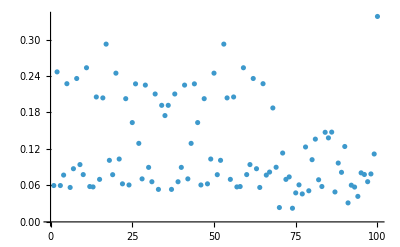

```mathematica
ListPlot[makeNearestTable[{8,8,3,1},EuclideanDistance,100],PlotRange->All]
```

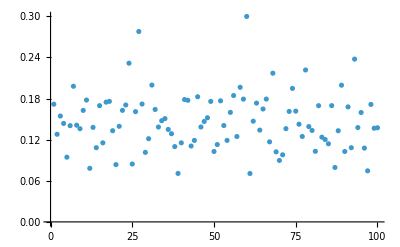

```mathematica
ListPlot[makeNearestTable[{9,3,3,3,2},EuclideanDistance,100],PlotRange->All]
```

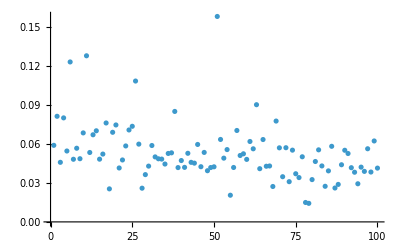

```mathematica
ListPlot[makeNearestTable[{7, 7, 3, 1, 1, 1},EuclideanDistance,100],PlotRange->All]
```

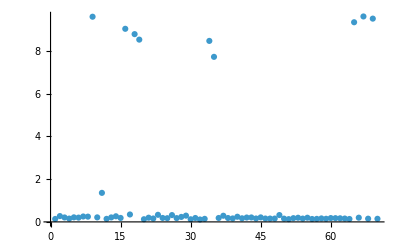

```mathematica
ListPlot[makeNearestTable[{10,2,2,2,2,2},EuclideanDistance,70],PlotRange->All]
```

### Nearest (Cosine distance)

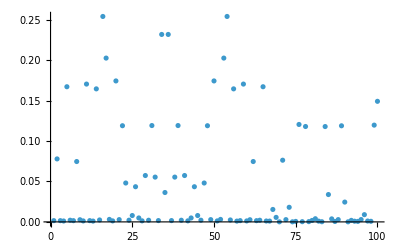

```mathematica
ListPlot[makeNearestTable[{8,8,3,1},CosineDistance,100],PlotRange->All]
```

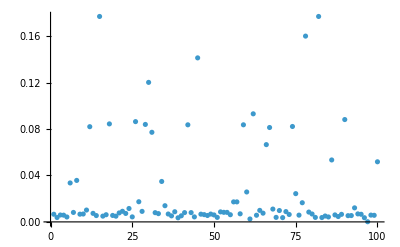

```mathematica
ListPlot[makeNearestTable[{9,3,3,3,2},CosineDistance,100],PlotRange->All]
```

```mathematica
PlotRootsComparison[{9,3,3,3,2},75,1]
```

-Graphics-

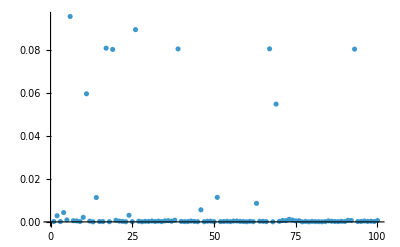

```mathematica
ListPlot[makeNearestTable[{7, 7, 3, 1, 1, 1},CosineDistance,100],PlotRange->All]
```

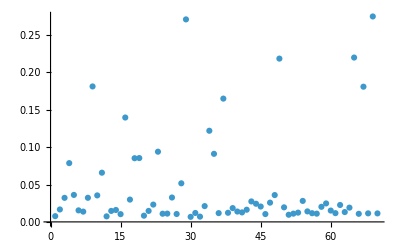

```mathematica
ListPlot[makeNearestTable[{10,2,2,2,2,2},CosineDistance,70],PlotRange->All]
```

### Machine learning and clusters (Max)

```mathematica
makeClusterTable[yd_,range_] := ParallelTable[
  loaddata[yd, rigg];
  
  clusterdata = Table[
    FindClusters[
      Join[ReIm /@ lazyroots[[k]], ReIm /@ stringroots[[k]]],
      Length[lazyroots[[k]]],
      Method -> "Agglomerate"
    ],
    {k, Length[lazyroots]}
  ];
  
  Countclusterdata = Table[
    Length /@ clusterdata[[k]],
    {k, Length[lazyroots]}
  ];
  
  MeanCountclusterdata = Countclusterdata // Flatten // Max // N;
  
  {rigg, MeanCountclusterdata, Countclusterdata},
  
  {rigg, 1, range, 1}
]
```

```mathematica
tableClusters=makeClusterTable[{7,7,3,1,1,1},100][[All,{1,2}]]
```

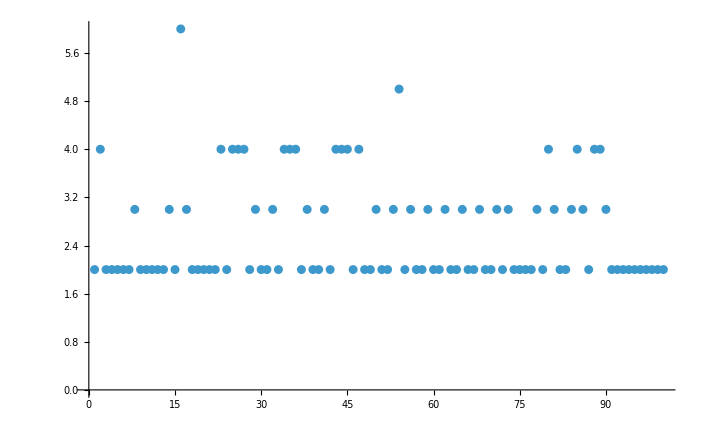

```mathematica
ListPlot[makeClusterTable[{8,8,3,1},100][[All,{1,2}]],PlotRange->All]
```

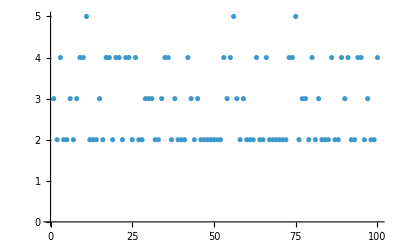

```mathematica
ListPlot[makeClusterTable[{9,3,3,3,2},100][[All,{1,2}]],PlotRange->All]
```

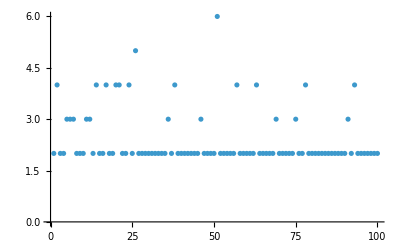

```mathematica
ListPlot[makeClusterTable[{7,7,3,1,1,1},100][[All,{1,2}]],PlotRange->All]
```

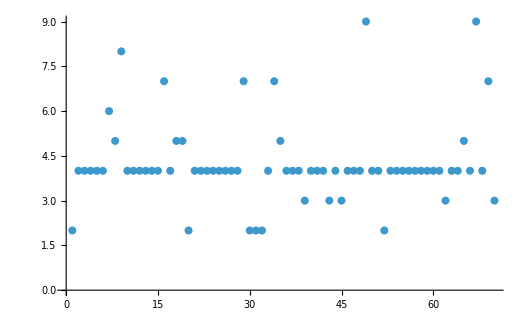

```mathematica
ListPlot[makeClusterTable[{10,2,2,2,2,2},70][[All,{1,2}]],PlotRange->All]
```

### Machine learning and clusters (Min) Boole

```mathematica
makeClusterTable[yd_,range_] := ParallelTable[
  loaddata[yd, rigg];
  
  clusterdata = Table[
    FindClusters[
      Join[ReIm /@ lazyroots[[k]], ReIm /@ stringroots[[k]]],
      Length[lazyroots[[k]]],
      Method -> "Agglomerate"
    ],
    {k, Length[lazyroots]}
  ];
  
  Countclusterdata = Table[
    Length /@ clusterdata[[k]],
    {k, Length[lazyroots]}
  ];
  
  MeanCountclusterdata = Countclusterdata // Flatten // Min // N;
  
  {rigg, MeanCountclusterdata, Countclusterdata},
  
  {rigg, 1, range, 1}
]
```

```mathematica
tableClusters=makeClusterTable[{7,7,3,1,1,1},100][[All,{1,2}]]
```

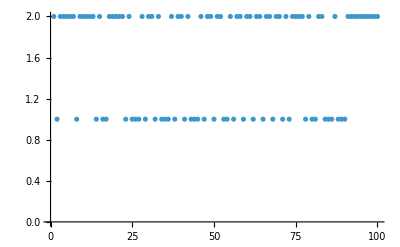

```mathematica
ListPlot[makeClusterTable[{8,8,3,1},100][[All,{1,2}]],PlotRange->All]
```

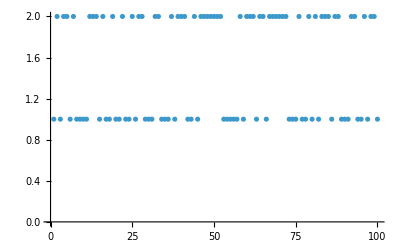

```mathematica
ListPlot[makeClusterTable[{9,3,3,3,2},100][[All,{1,2}]],PlotRange->All]
```

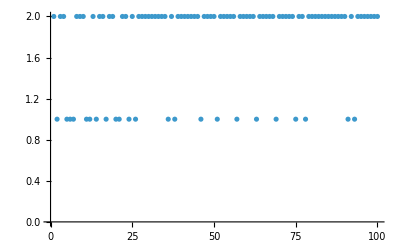

```mathematica
ListPlot[makeClusterTable[{7,7,3,1,1,1},100][[All,{1,2}]],PlotRange->All]
```

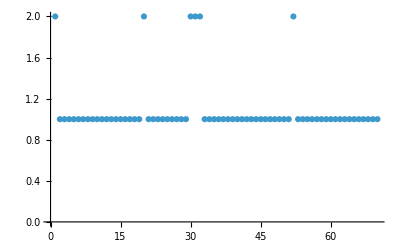

```mathematica
ListPlot[makeClusterTable[{10,2,2,2,2,2},70][[All,{1,2}]],PlotRange->All]
```

### HausdorffDistance NoFlatten

```mathematica
data8831 = Table[HausdorffDistanceBetweenRootsM[{8,8,3,1},k],{k,1,100}];
data93332 = Table[HausdorffDistanceBetweenRootsM[{9,3,3,3,2},k],{k,1,100}];
data773111 = Table[HausdorffDistanceBetweenRootsM[{7, 7, 3, 1, 1, 1},k],{k,1,100}];
data1022222 = Table[HausdorffDistanceBetweenRootsM[{10,2,2,2,2,2},k],{k,1,70}];
```

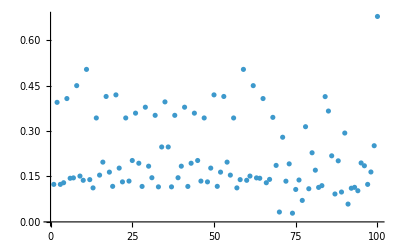

```mathematica
ListPlot[Mean/@data8831,PlotRange->All]
```

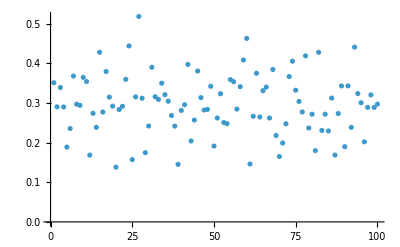

```mathematica
ListPlot[Mean/@data93332,PlotRange->All]
```

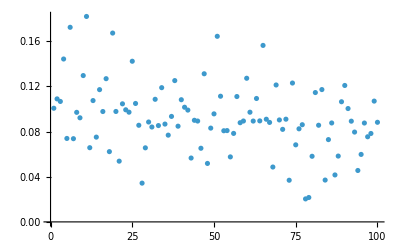

```mathematica
ListPlot[Mean/@data773111,PlotRange->All]
```

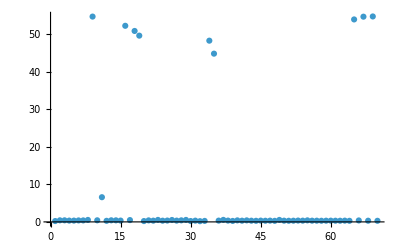

```mathematica
ListPlot[Mean/@data1022222,PlotRange->All]
```

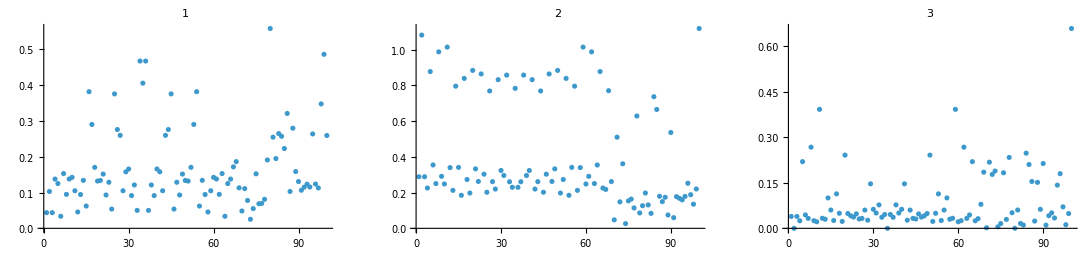

```mathematica
GraphicsRow[ListPlot[#,PlotLabel->" "<>ToString[#2],PlotRange->All]&@@@Transpose[{Transpose[data8831],Range[Length[data8831[[1]]]]}]]
```

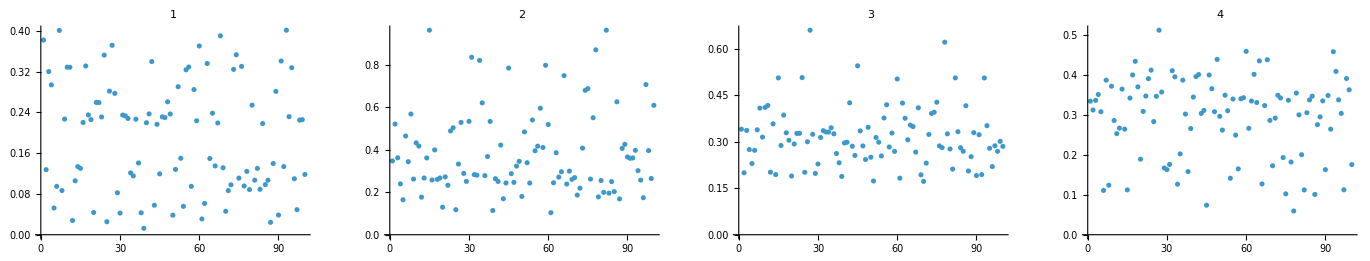

```mathematica
GraphicsRow[ListPlot[#,PlotLabel->" "<>ToString[#2],PlotRange->All]&@@@Transpose[{Transpose[data93332],Range[Length[data93332[[1]]]]}]]
```

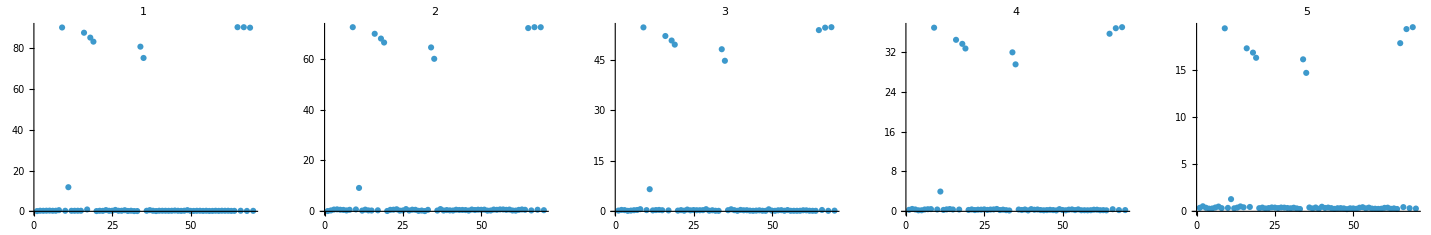

```mathematica
GraphicsRow[ListPlot[#,PlotLabel->" "<>ToString[#2],PlotRange->All]&@@@Transpose[{Transpose[data1022222],Range[Length[data1022222[[1]]]]}]]
```

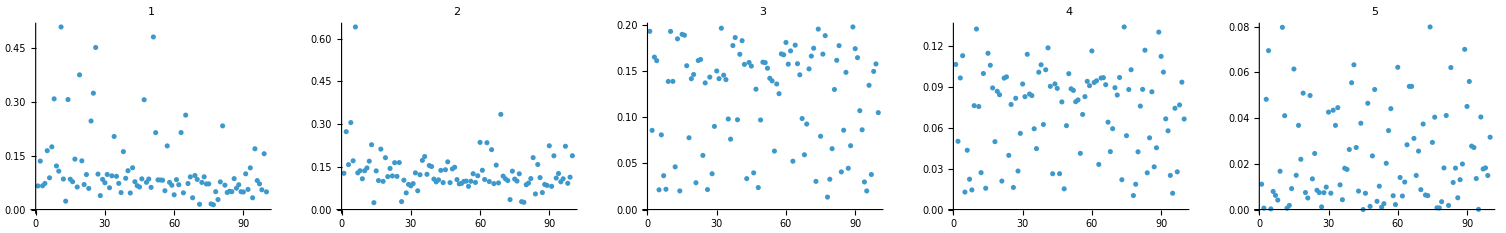

```mathematica
GraphicsRow[ListPlot[#,PlotLabel->" "<>ToString[#2],PlotRange->All]&@@@Transpose[{Transpose[data773111],Range[Length[data773111[[1]]]]}]]
```

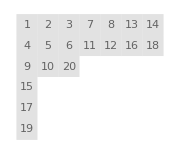
Rigg: 4164.
Hausdorff Distance: 0.19282
Rigged Configuration:
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ∅
Standard Young Tableau:
-Graphics-

```mathematica
RiggConfiguration[{7, 7, 3, 1, 1, 1},10]
```

### HausdorffDistance Flatten mean

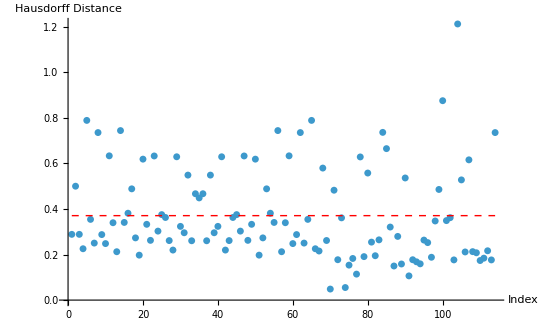

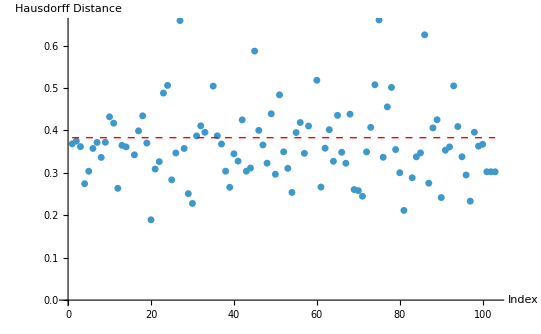

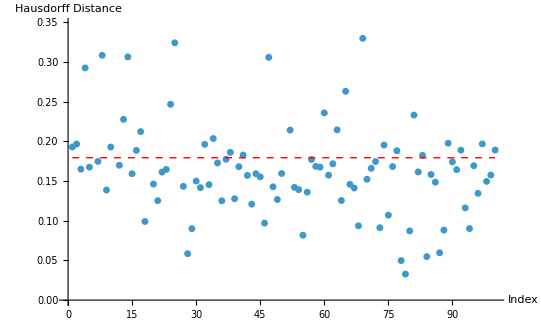

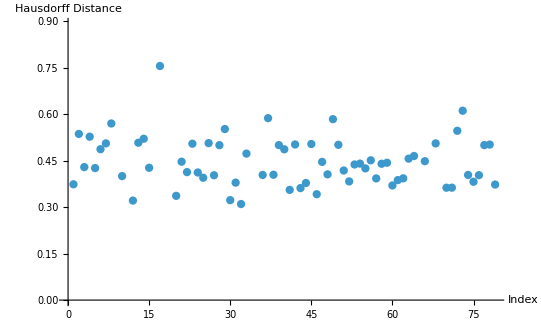

```mathematica
PlotHausdorffDistanceWithMean[{8,8,3,1}]
PlotHausdorffDistanceWithMean[{9,3,3,3,2}]
PlotHausdorffDistanceWithMean[{7, 7, 3, 1, 1, 1}]
PlotHausdorffDistanceWithMean[{10,2,2,2,2,2}]
```

### Individual data visualization

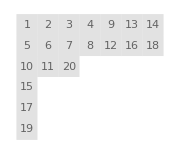
Rigg: 4167.
Hausdorff Distance: 0.19291
Rigged Configuration:
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ∅
Standard Young Tableau:
-Graphics-

```mathematica
RiggConfiguration[{7, 7, 3, 1, 1, 1},1]
```

```mathematica
(*index = 0 -> all roots*)
PlotRootsComparison[{7, 7, 3, 1, 1, 1},24,0]
```

-Graphics-

### All exact Bethe roots visualization

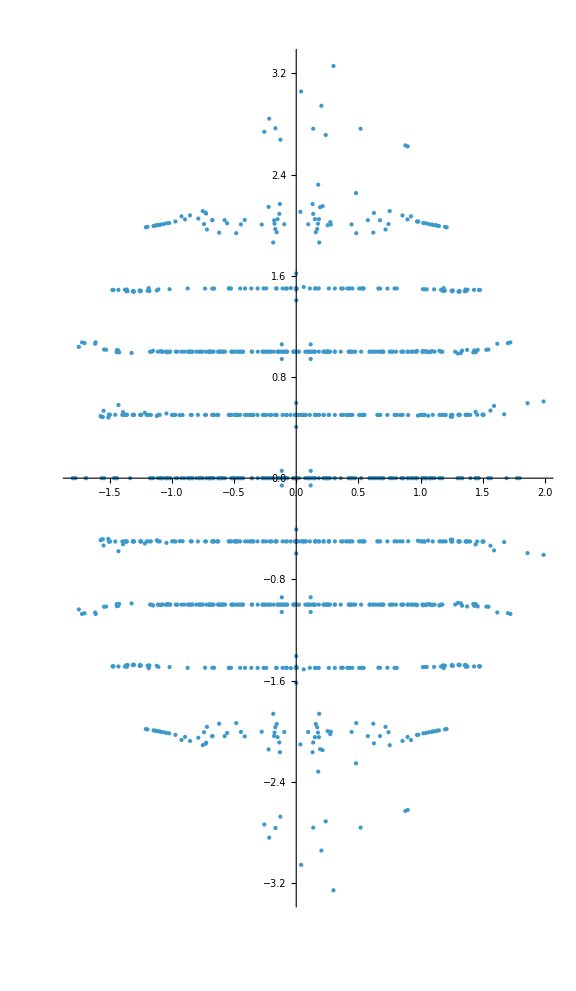

```mathematica
plots = Table[
   loaddata[{8,8,3,1}, yd];
   ComplexListPlot[
    lazyroots[[1]],
     PlotStyle -> PointSize[Small]
   ],
   {yd, 1, 100}
   ];

Show[plots, PlotRange -> All, ImageSize -> Large]
```

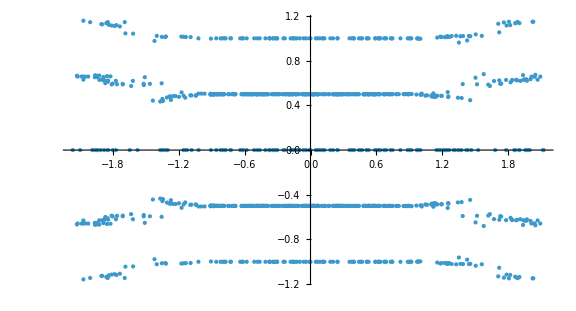

```mathematica
plots = Table[
   loaddata[{9, 3, 3, 3, 2}, yd];
   ComplexListPlot[
     lazyroots[[1]],
     PlotStyle -> PointSize[Small]
   ],
   {yd, 1, 100}
   ];

Show[plots, PlotRange -> All, ImageSize -> Large]
```

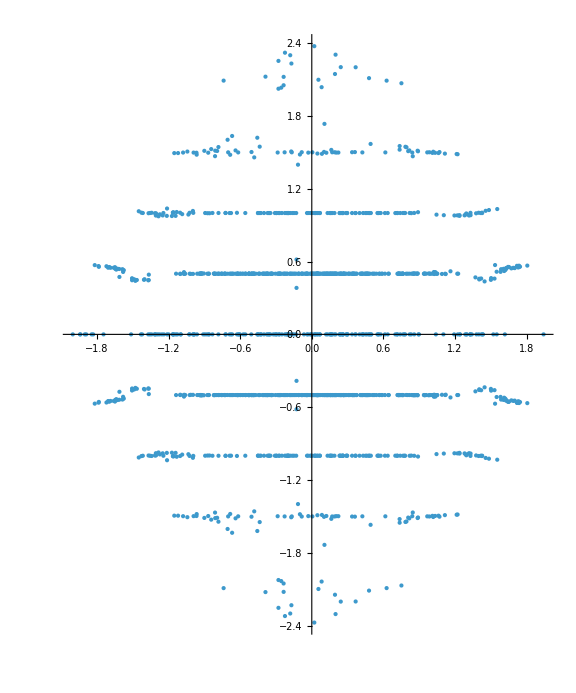

```mathematica
plots = Table[
   loaddata[{7, 7, 3, 1, 1, 1}, yd];
   ComplexListPlot[
     lazyroots[[1]],
     PlotStyle -> PointSize[Small]
   ],
   {yd, 1, 100}
   ];

Show[plots, PlotRange -> All, ImageSize -> Large]
```

```mathematica
.b4
```